```mathematica
(*s=InputString["Enter xml file name","tooth.xml"]//StringReplace[#," "->""]&;*)
(*xml=Import[NotebookDirectory[]<>"~images\\"<>"nucleon_naive.xml"];*)
(*xml=Import[NotebookDirectory[]<>"~images\\"<>"nucleon_strong_red.xml"];*)
(*xml=Import[NotebookDirectory[]<>"~images\\"<>"nucleon_weak_red.xml"];*)
(*xml=Import[NotebookDirectory[]<>"~images\\"<>"nucleon_naive_optimized_green_1000.xml"];*)
(*xml=Import[NotebookDirectory[]<>"~images\\"<>"nucleon_naive_optimized_red_1000.xml"];*)
xml=Import[NotebookDirectory[]<>"~images\\"<>"vismale_strong_green.xml"];
{tfifile,volumefile,legends,face,imagefilenames,txtfilenames,{featurefilename,visibilityfilename},resultxml,imagefile,rawfile,dataname,plotpath,imagepath}=xml;
(*Column[xml,Background->{{Lighter@LightYellow,Lighter@LightBlue}},Frame->True,FrameStyle->Directive[LightGray,Thin,Dashed]]*)

tf=Import[tfifile,"XML"];
bincount=256;
intensity=ToExpression@Cases[tf,XMLElement["intensity",{"value"->atrib_,___},___]:>atrib,∞];
r=ToExpression@Cases[tf,XMLElement["colorL",{"r"->atrib_,___},___]:>atrib,∞];
g=ToExpression@Cases[tf,XMLElement["colorL",{___,"g"->atrib_,___},___]:>atrib,∞];
b=ToExpression@Cases[tf,XMLElement["colorL",{___,"b"->atrib_,___},___]:>atrib,∞];
a=ToExpression@Cases[tf,XMLElement["colorL",{___,"a"->atrib_},___]:>atrib,∞];
rgbcolors=(#/255.&)/@Transpose[{r,g,b}]//(RGBColor/@#&);
rgbfunction=(Blend[Transpose[{intensity,rgbcolors}], #1] & );
rgba=(#/255.&)/@Transpose[{r,g,b,a}]//(RGBColor/@#&);
rgbafunction=(Blend[Transpose[{intensity,rgba}], #1] & );
alpha=(#/255.&)/@a;

d = Import[volumefile,"Image3D"];
colorized=Image3D[d,ColorFunction->rgbafunction];
{lightness,chroma,hue,opacity}=ImageApply[List@@rgbafunction[#]&,d]//Image3D[#,ColorSpace->"RGB"]&//ColorSeparate[ColorConvert[#,"LCH"]]&;
(*lo=ImageMultiply[lightness,opacity];
co=ImageMultiply[chroma,opacity];*)
(*g1=ImageDifference[GaussianFilter[lightness,{2,Sqrt[2]/8.*2}],GaussianFilter[lightness,{4,Sqrt[2]/8.*4}]]
g2=ImageDifference[GaussianFilter[chroma,{2,Sqrt[2]/8.*2}],GaussianFilter[chroma,{4,Sqrt[2]/8.*4}]]
g3=ImageDifference[GaussianFilter[hue,{2,Sqrt[2]/8.*2}],GaussianFilter[hue,{4,Sqrt[2]/8.*4}]];
g4=ImageDifference[GaussianFilter[opacity,{2,Sqrt[2]/8.*2}],GaussianFilter[opacity,{4,Sqrt[2]/8.*4}]];*)
{g1,g2}=ParallelMap[ImageDifference[GaussianFilter[#,{2,Sqrt[2]/8.*2}],GaussianFilter[#,{4,Sqrt[2]/8.*4}]]&,{lightness,chroma}];

pos=intensity[[#]]&/@Flatten@Position[alpha,_?(#==0&)];
index=Flatten@Position[alpha,_?(#>0&)];
features=Table[ImageApply[If[#≥pos[[i]] && #≤pos[[i+1]],1,0]&,d],{i,1,Length[pos],2}];
chartcolors=rgbcolors[[#]]&/@index;
colorizedfeatures=ImageMultiply[colorized,#]&/@features;
viewpoints=<|"top":>Top,"back":>Back,"left":>Left,"bottom":>Bottom,"front":>Front,"right":>Right|>;
MapIndexed[Export[StringReplace[imagefile,"."->"_"<>ToString[First[#2]]<>"."],Show[#,Boxed->False,ViewPoint->viewpoints[face]]]&,colorizedfeatures];

intensity0=intensity;
alpha0=alpha;
rangeOfAlpha=Range[Length[alpha]];
If[First[intensity0]>0,intensity0=Join[{0},intensity0];alpha0=Join[{0},alpha0];rangeOfAlpha+=1];
If[Last[intensity0]<1,intensity0=Join[intensity0,{1}];alpha0=Join[alpha0,{0}]];
(*ListLinePlot[Transpose[{intensity0,alpha0}],PlotRange->{{0,1},{0,1}},ColorFunction->rgbfunction,PlotLegends->"user specified transfer function"]*)
(*fun=Interpolation[Transpose[{intensity0,alpha0}],InterpolationOrder->1];*)
(*Plot[fun[x],{x,0,1},PlotRange->{{0,1},{0,1}},ColorFunction->rgbfunction,PlotLegends->"user specified transfer function"]*)
index0=Flatten@Position[alpha0,_?(#>0&)];

targets=<|2->{0.2,0.8},3->{0.1,0.3,0.6},4->{0.1,0.2,0.3,0.4}|>;
target=targets[Length[index0]]
CloseKernels[];
LaunchKernels[8];
Clear[f];
Clear[data];
records={};
epsilon=0.01;
stepsize=0.05;
```

{0.1,0.3,0.6}

```mathematica
top:=Module[{list,count,img,list2,list3,d1},(* top *)
list=Image3DSlices[data,All,1];
count=Length[list];
img=First[list];
list2=Table[img=ImageApply[#1+Clip[1-#1,{0,1}]*f[#2]&,{img,list[[i]]}],{i,2,count}]//Join[{First[list]},#]&;
list3=Table[ImageSubtract[list2[[i]],list2[[i-1]]],{i,2,count}]//Join[{First[list]},#]&;
d1=Image3D[list3]]
back:=Module[{list,count,img,list2,list3,tmp,d2},(* back *)
list=Image3DSlices[data,All,2];
count=Length[list];
img=First[list];
list2=Table[img=ImageApply[#1+Clip[1-#1,{0,1}]*f[#2]&,{img,list[[i]]}],{i,2,count}]//Join[{First[list]},#]&;
list3=Table[ImageSubtract[list2[[i]],list2[[i-1]]],{i,2,count}]//Join[{First[list]},#]&;
tmp=Image3D[Reverse[list3]];
d2=ImageRotate[tmp,{90 Degree,{1,0,0}}]]
left:=Module[{list,count,img,list2,list3,tmp,d3},(* left *)
list=Image3DSlices[data,All,3];
count=Length[list];
img=First[list];
list2=Table[img=ImageApply[#1+Clip[1-#1,{0,1}]*f[#2]&,{img,list[[i]]}],{i,2,count}]//Join[{First[list]},#]&;
list3=Table[ImageSubtract[list2[[i]],list2[[i-1]]],{i,2,count}]//Join[{First[list]},#]&;
tmp=Image3D[list3];
d3=ImageRotate[tmp,{90 Degree,{1,0,0}}]//ImageRotate[#,-90 Degree]&]
bottom:=Module[{list,count,img,list2,list3,d4},(* bottom *)
list=Reverse@Image3DSlices[data,All,1];
count=Length[list];
img=First[list];
list2=Table[img=ImageApply[#1+Clip[1-#1,{0,1}]*f[#2]&,{img,list[[i]]}],{i,2,count}]//Join[{First[list]},#]&;
list3=Table[ImageSubtract[list2[[i]],list2[[i-1]]],{i,2,count}]//Join[{First[list]},#]&;
d4=Image3D[Reverse[list3]]]
front:=Module[{list,count,img,list2,list3,tmp,d5},(* front *)
list=Reverse@Image3DSlices[data,All,2];
count=Length[list];
img=First[list];
list2=Table[img=ImageApply[#1+Clip[1-#1,{0,1}]*f[#2]&,{img,list[[i]]}],{i,2,count}]//Join[{First[list]},#]&;
list3=Table[ImageSubtract[list2[[i]],list2[[i-1]]],{i,2,count}]//Join[{First[list]},#]&;
tmp=Image3D[list3];
d5=ImageRotate[tmp,{90 Degree,{1,0,0}}]]
right:=Module[{list,count,img,list2,list3,tmp,d6},(* right *)
list=Reverse@Image3DSlices[data,All,3];
count=Length[list];
img=First[list];
list2=Table[img=ImageApply[#1+Clip[1-#1,{0,1}]*f[#2]&,{img,list[[i]]}],{i,2,count}]//Join[{First[list]},#]&;
list3=Table[ImageSubtract[list2[[i]],list2[[i-1]]],{i,2,count}]//Join[{First[list]},#]&;
tmp=Image3D[Reverse[list3]];
d6=ImageRotate[tmp,{90 Degree,{1,0,0}}]//ImageRotate[#,-90 Degree]&]
renderslices=<|"top":>top,"back":>back,"left":>left,"bottom":>bottom,"front":>front,"right":>right|>;
```

```mathematica
top2:=Module[{list,img,list2,list3,df,d1},(* top *)
df=ImageApply[f[#]&,data];
list=Image3DSlices[df,All,1];
img=First[list];
list2=Table[img=ImageAdd[img,ImageMultiply[ImageClip@ColorNegate[img],i]],{i,list[[2;;]]}]//Prepend[#,First[list]]&;
list3=Table[ImageSubtract[list2[[i]],list2[[i-1]]],{i,2,Length[list]}]//Prepend[#,First[list]]&;
d1=Image3D[list3]
]
back2:=Module[{list,img,list2,list3,tmp,df,d2},(* back *)
df=ImageApply[f[#]&,data];
list=Image3DSlices[df,All,2];
img=First[list];
list2=Table[img=ImageAdd[img,ImageMultiply[ImageClip@ColorNegate[img],i]],{i,list[[2;;]]}]//Prepend[#,First[list]]&;
list3=Table[ImageSubtract[list2[[i]],list2[[i-1]]],{i,2,Length[list]}]//Prepend[#,First[list]]&;
tmp=Image3D[Reverse[list3]];
d2=ImageRotate[tmp,{90 Degree,{1,0,0}}]]
left2:=Module[{list,img,list2,list3,tmp,df,d3},(* left *)
df=ImageApply[f[#]&,data];
list=Image3DSlices[df,All,3];
img=First[list];
list2=Table[img=ImageAdd[img,ImageMultiply[ImageClip@ColorNegate[img],i]],{i,list[[2;;]]}]//Prepend[#,First[list]]&;
list3=Table[ImageSubtract[list2[[i]],list2[[i-1]]],{i,2,Length[list]}]//Prepend[#,First[list]]&;
tmp=Image3D[list3];
d3=ImageRotate[tmp,{90 Degree,{1,0,0}}]//ImageRotate[#,-90 Degree]&]
bottom2:=Module[{list,img,list2,list3,df,d4},(* bottom *)
df=ImageApply[f[#]&,data];
list=Reverse@Image3DSlices[df,All,1];
img=First[list];
list2=Table[img=ImageAdd[img,ImageMultiply[ImageClip@ColorNegate[img],i]],{i,list[[2;;]]}]//Prepend[#,First[list]]&;
list3=Table[ImageSubtract[list2[[i]],list2[[i-1]]],{i,2,Length[list]}]//Prepend[#,First[list]]&;
d4=Image3D[Reverse[list3]]]
front2:=Module[{list,img,list2,list3,tmp,df,d5},(* front *)
df=ImageApply[f[#]&,data];
list=Reverse@Image3DSlices[df,All,2];
img=First[list];
list2=Table[img=ImageAdd[img,ImageMultiply[ImageClip@ColorNegate[img],i]],{i,list[[2;;]]}]//Prepend[#,First[list]]&;
list3=Table[ImageSubtract[list2[[i]],list2[[i-1]]],{i,2,Length[list]}]//Prepend[#,First[list]]&;
tmp=Image3D[list3];
d5=ImageRotate[tmp,{90 Degree,{1,0,0}}]]
right2:=Module[{list,img,list2,list3,tmp,df,d6},(* right *)
df=ImageApply[f[#]&,data];
list=Reverse@Image3DSlices[df,All,3];
img=First[list];
list2=Table[img=ImageAdd[img,ImageMultiply[ImageClip@ColorNegate[img],i]],{i,list[[2;;]]}]//Prepend[#,First[list]]&;
list3=Table[ImageSubtract[list2[[i]],list2[[i-1]]],{i,2,Length[list]}]//Prepend[#,First[list]]&;
tmp=Image3D[Reverse[list3]];
d6=ImageRotate[tmp,{90 Degree,{1,0,0}}]//ImageRotate[#,-90 Degree]&]
renderslices2=<|"top":>top2,"back":>back2,"left":>left2,"bottom":>bottom2,"front":>front2,"right":>right2|>;
```

```mathematica
VisibilitySaliency[peaks_]:=Module[{alpha2,fun,vis,viss,vs,mean,total},
alpha2=alpha0;
MapIndexed[(alpha2[[#]]=peaks[[First@#2]])&,index0];
fun=Interpolation[Transpose[{intensity0,alpha2}],InterpolationOrder->1];
vis=Block[{f=fun,data=d},renderslices2[face]];
viss=Map[ImageMultiply[#,vis]&,{g1,g2}];
total=Map[ImageMeasurements[#,"TotalIntensity"]&,viss];
vs=Table[Table[If[total[[j]]≠0,ImageMeasurements[ImageMultiply[viss[[j]],i],"TotalIntensity"]/total[[j]],0],{i,features}],{j,Length[total]}];
mean=Mean[vs]
]
Visibility[fun_]:=Module[{vis,viss,vs,mean,total},
vis=Block[{f=fun,data=d},renderslices2[face]];
viss=Map[ImageMultiply[#,vis]&,{g1,g2}];
total=Map[ImageMeasurements[#,"TotalIntensity"]&,viss];
vs=Table[Table[If[total[[j]]≠0,ImageMeasurements[ImageMultiply[viss[[j]],i],"TotalIntensity"]/total[[j]],0],{i,features}],{j,Length[total]}];
mean=Mean[vs]
]
```

```mathematica
(* x(k+1)=x(k)-(f-f0)/(f'-f0') *)
(*reset peak control points*)
alpha0[[#]]&/@index0;
peaks=alpha[[#]]&/@index;
MapIndexed[(alpha0[[#]]=peaks[[First@#2]])&,index0];
(*gradient descent with fixed step size*)
iteration=0;
previous={0,{0,0,0},{0,0,0}};
t1=AbsoluteTime[];
t2=0;
list=Table[Module[{peaks,mean,steps,rms,peaks0,gradient,direction,square},
mean=Visibility[Interpolation[Transpose[{intensity0,alpha0}],InterpolationOrder->1]];
rms=RootMeanSquare[mean-target];
peaks=alpha0[[#]]&/@index0;
gradient:=2*(mean-target);
square:=(mean-target)^2;
steps=If[First@previous==0,-gradient*stepsize,Module[{rms0,mean0,p0,g0,s0,dy,dx},
{rms0,mean0,p0,g0,s0}=previous;
dy=square-s0;
dx=gradient-g0;
If[Product[i,{i,dx}]≠0,direction=Normalize[dy/dx]*Norm[gradient];-direction*stepsize,-gradient*stepsize]
]];
previous={rms,mean,peaks,gradient,square};
peaks0=peaks;
peaks=Clip[peaks+steps,{0,1}];
MapIndexed[(alpha0[[#]]=peaks[[First@#2]])&,index0];
If[t2==0 && rms<epsilon,t2=AbsoluteTime[];iteration=iterator];
{mean,peaks0,rms,steps,gradient,direction}
],{iterator,50}];
```

-3.6537587901661791×10^9

0

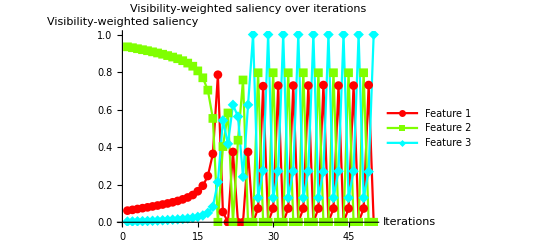

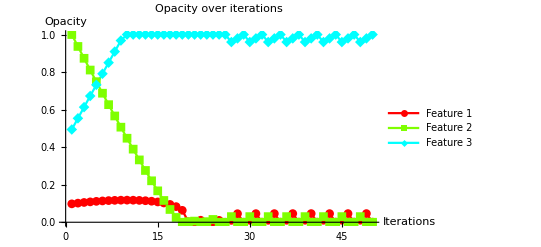

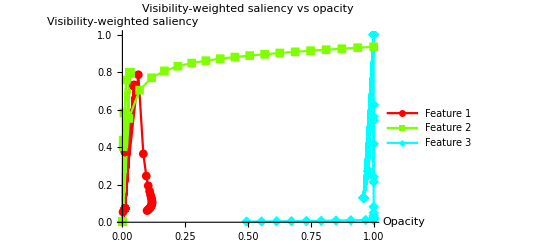

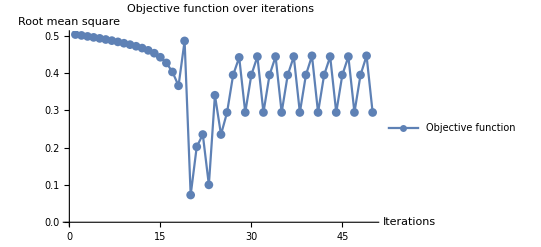

| Visibility-Weighted Saliency | Opacity | Root Mean Square | Steps |  | 
1 | 0.0619607
0.934603
0.00343598 | 0.0980392
1.
0.494118 | 0.503341 | 0.00380393
-0.0634603
0.0596564 | -0.0760786
1.26921
-1.19313 | direction$2093
2 | 0.0659797
0.929892
0.00412778 | 0.101843
0.93654
0.553774 | 0.500994 | 0.00359457
-0.0630773
0.0594827 | -0.0680406
1.25978
-1.19174 | -0.0718914
1.26155
-1.18965
3 | 0.0706084
0.924502
0.00488963 | 0.105438
0.873462
0.613257 | 0.498338 | 0.00316218
-0.0625533
0.0593912 | -0.0587831
1.249
-1.19022 | -0.0632436
1.25107
-1.18782
4 | 0.0749978
0.919252
0.00574991 | 0.1086
0.810909
0.672648 | 0.495726 | 0.00271255
-0.0620246
0.059312 | -0.0500043
1.2385
-1.1885 | -0.054251
1.24049
-1.18624
5 | 0.0794324
0.913898
0.00666943 | 0.111312
0.748885
0.73196 | 0.493064 | 0.00227236
-0.0614918
0.0592195 | -0.0411351
1.2278
-1.18666 | -0.0454473
1.22984
-1.18439
6 | 0.0843328
0.907891
0.00777633 | 0.113585
0.687393
0.791179 | 0.49007 | 0.00180623
-0.0609038
0.0590976 | -0.0313345
1.21578
-1.18445 | -0.0361247
1.21808
-1.18195
7 | 0.0891531
0.90185
0.00899678 | 0.115391
0.626489
0.850277 | 0.487041 | 0.00132161
-0.0602999
0.0589783 | -0.0216939
1.2037
-1.18201 | -0.0264321
1.206
-1.17957
8 | 0.0944794
0.895144
0.0103767 | 0.116713
0.566189
0.909255 | 0.483695 | 0.00081556
-0.0596439
0.0588283 | -0.0110411
1.19029
-1.17925 | -0.0163112
1.19288
-1.17657
9 | 0.10019
0.887836
0.0119731 | 0.117528
0.506545
0.968084 | 0.480044 | 0.000265496
-0.0589255
0.05866 | 0.000380997
1.17567
-1.17605 | -0.00530992
1.17851
-1.1732
10 | 0.106277
0.880088
0.0136353 | 0.117794
0.44762
1. | 0.476223 | -0.000322086
-0.0581634
0.0584855 | 0.012554
1.16018
-1.17273 | 0.00644173
1.16327
-1.16971
11 | 0.113515
0.871163
0.0153223 | 0.117472
0.389456
1. | 0.471967 | -0.000985178
-0.057305
0.0582902 | 0.0270302
1.14233
-1.16936 | 0.0197036
1.1461
-1.1658
12 | 0.121875
0.860716
0.0174095 | 0.116486
0.332151
1. | 0.467009 | -0.00176018
-0.0562963
0.0580565 | 0.0437493
1.12143
-1.16518 | 0.0352036
1.12593
-1.16113
13 | 0.132015
0.847894
0.0200907 | 0.114726
0.275855
1. | 0.46098 | -0.00267708
-0.0550721
0.0577492 | 0.0640306
1.09579
-1.15982 | 0.0535416
1.10144
-1.15498
14 | 0.145134
0.831271
0.0235952 | 0.112049
0.220783
1. | 0.453331 | -0.00382543
-0.0535099
0.0573353 | 0.0902685
1.06254
-1.15281 | 0.0765085
1.0702
-1.14671
15 | 0.165176
0.806357
0.028467 | 0.108224
0.167273
1. | 0.442453 | -0.00544932
-0.0512587
0.056708 | 0.130352
1.01271
-1.14307 | 0.108986
1.02517
-1.13416
16 | 0.194348
0.769569
0.0360825 | 0.102774
0.116014
1. | 0.427161 | -0.00783865
-0.0479547
0.0557934 | 0.188696
0.939139
-1.12784 | 0.156773
0.959094
-1.11587
17 | 0.246447
0.703799
0.0497536 | 0.0949358
0.0680595
1. | 0.403018 | -0.0117052
-0.0424548
0.0541599 | 0.292895
0.807598
-1.10049 | 0.234103
0.849095
-1.0832
18 | 0.364479
0.553096
0.0824246 | 0.0832306
0.0256048
1. | 0.366011 | -0.0197455
-0.0315645
0.05131 | 0.528959
0.506192
-1.03515 | 0.394909
0.63129
-1.0262
19 | 0.785841
0.
0.214159 | 0.0634852
0.
1. | 0.486228 | -0.0609987
0.00301064
0.0579881 | 1.37168
-0.6
-0.771683 | 1.21997
-0.0602128
-1.15976
20 | 0.0547761
0.402999
0.542225 | 0.00248646
0.00301064
1. | 0.0730114 | -0.0100794
0.00309959
0.00697982 | -0.0904478
0.205998
-0.11555 | 0.201588
-0.0619918
-0.139596
21 | 0.
0.582193
0.417807 | 0.
0.00611023
1. | 0.202342 | 0.0106814
-0.0283312
0.0176499 | -0.2
0.564385
-0.364385 | -0.213627
0.566625
-0.352997
22 | 0.374479
0.
0.625521 | 0.0106814
0.
1. | 0.235223 | -0.0302272
0.00308501
0.0271422 | 0.548958
-0.6
0.051042 | 0.604544
-0.0617002
-0.542844
23 | 0.
0.437127
0.562873 | 0.
0.00308501
1. | 0.100303 | -0.0126847
0.011841
0.000843771 | -0.2
0.274254
-0.0742542 | 0.253695
-0.236819
-0.0168754
24 | 0.
0.757968
0.242032 | 0.
0.014926
1. | 0.340527 | 0.01
-0.0457968
0.0357968 | -0.2
0.915935
-0.715935 | direction$32618
25 | 0.374479
0.
0.625521 | 0.01
0.
1. | 0.235223 | -0.0174517
-0.0158002
0.0332519 | 0.548958
-0.6
0.051042 | 0.349034
0.316004
-0.665039
26 | 0.
0.
1. | 0.
0.
1. | 0.294392 | 0.01
0.03
-0.04 | -0.2
-0.6
0.8 | direction$35272
27 | 0.073244
0.796452
0.130304 | 0.01
0.03
0.96 | 0.394882 | 0.0355363
-0.0550757
0.0195394 | -0.0535121
0.992904
-0.939392 | -0.710726
1.10151
-0.390788
28 | 0.724956
0.
0.275044 | 0.0455363
0.
0.979539 | 0.442028 | -0.0451731
-0.0148351
0.0600082 | 1.24991
-0.6
-0.649912 | 0.903462
0.296701
-1.20016
29 | 0.
0.
1. | 0.00036321
0.
1. | 0.294392 | 0.01
0.03
-0.04 | -0.2
-0.6
0.8 | direction$39253
30 | 0.073244
0.796452
0.130304 | 0.0103632
0.03
0.96 | 0.394882 | 0.0355363
-0.0550757
0.0195394 | -0.0535121
0.992904
-0.939392 | -0.710726
1.10151
-0.390788
31 | 0.72802
0.
0.27198 | 0.0458995
0.
0.979539 | 0.444224 | -0.0454414
-0.0148471
0.0602885 | 1.25604
-0.6
-0.65604 | 0.908827
0.296943
-1.20577
32 | 0.
0.
1. | 0.000458137
0.
1. | 0.294392 | 0.01
0.03
-0.04 | -0.2
-0.6
0.8 | direction$43234
33 | 0.073244
0.796452
0.130304 | 0.0104581
0.03
0.96 | 0.394882 | 0.0355363
-0.0550757
0.0195394 | -0.0535121
0.992904
-0.939392 | -0.710726
1.10151
-0.390788
34 | 0.72802
0.
0.27198 | 0.0459944
0.
0.979539 | 0.444224 | -0.0454414
-0.0148471
0.0602885 | 1.25604
-0.6
-0.65604 | 0.908827
0.296943
-1.20577
35 | 0.
0.
1. | 0.000553063
0.
1. | 0.294392 | 0.01
0.03
-0.04 | -0.2
-0.6
0.8 | direction$47215
36 | 0.073244
0.796452
0.130304 | 0.0105531
0.03
0.96 | 0.394882 | 0.0355363
-0.0550757
0.0195394 | -0.0535121
0.992904
-0.939392 | -0.710726
1.10151
-0.390788
37 | 0.72802
0.
0.27198 | 0.0460894
0.
0.979539 | 0.444224 | -0.0454414
-0.0148471
0.0602885 | 1.25604
-0.6
-0.65604 | 0.908827
0.296943
-1.20577
38 | 0.
0.
1. | 0.00064799
0.
1. | 0.294392 | 0.01
0.03
-0.04 | -0.2
-0.6
0.8 | direction$51196
39 | 0.073244
0.796452
0.130304 | 0.010648
0.03
0.96 | 0.394882 | 0.0355363
-0.0550757
0.0195394 | -0.0535121
0.992904
-0.939392 | -0.710726
1.10151
-0.390788
40 | 0.730888
0.
0.269112 | 0.0461843
0.
0.979539 | 0.446283 | -0.0456929
-0.0148584
0.0605513 | 1.26178
-0.6
-0.661776 | 0.913857
0.297168
-1.21103
41 | 0.
0.
1. | 0.000491431
0.
1. | 0.294392 | 0.01
0.03
-0.04 | -0.2
-0.6
0.8 | direction$55177
42 | 0.073244
0.796452
0.130304 | 0.0104914
0.03
0.96 | 0.394882 | 0.0355363
-0.0550757
0.0195394 | -0.0535121
0.992904
-0.939392 | -0.710726
1.10151
-0.390788
43 | 0.72802
0.
0.27198 | 0.0460277
0.
0.979539 | 0.444224 | -0.0454414
-0.0148471
0.0602885 | 1.25604
-0.6
-0.65604 | 0.908827
0.296943
-1.20577
44 | 0.
0.
1. | 0.000586357
0.
1. | 0.294392 | 0.01
0.03
-0.04 | -0.2
-0.6
0.8 | direction$59158
45 | 0.073244
0.796452
0.130304 | 0.0105864
0.03
0.96 | 0.394882 | 0.0355363
-0.0550757
0.0195394 | -0.0535121
0.992904
-0.939392 | -0.710726
1.10151
-0.390788
46 | 0.72802
0.
0.27198 | 0.0461227
0.
0.979539 | 0.444224 | -0.0454414
-0.0148471
0.0602885 | 1.25604
-0.6
-0.65604 | 0.908827
0.296943
-1.20577
47 | 0.
0.
1. | 0.000681284
0.
1. | 0.294392 | 0.01
0.03
-0.04 | -0.2
-0.6
0.8 | direction$63139
48 | 0.073244
0.796452
0.130304 | 0.0106813
0.03
0.96 | 0.394882 | 0.0355363
-0.0550757
0.0195394 | -0.0535121
0.992904
-0.939392 | -0.710726
1.10151
-0.390788
49 | 0.730888
0.
0.269112 | 0.0462176
0.
0.979539 | 0.446283 | -0.0456929
-0.0148584
0.0605513 | 1.26178
-0.6
-0.661776 | 0.913857
0.297168
-1.21103
50 | 0.
0.
1. | 0.000524724
0.
1. | 0.294392 | 0.01
0.03
-0.04 | -0.2
-0.6
0.8 | direction$67120

```mathematica
t2-t1
iteration
saliency5=ListLinePlot[Transpose[#&@@@list],PlotLegends->{"Feature 1","Feature 2","Feature 3","Feature 4"},PlotLabel->"Visibility-weighted saliency over iterations",PlotRange->{All,{0,1}},PlotStyle->chartcolors,PlotMarkers->Automatic,AxesLabel->{"Iterations","Visibility-weighted saliency"}]
Export[plotpath<>dataname<>"_saliency_newton.png",saliency5];
opacity5=ListLinePlot[Transpose[#2&@@@list],PlotLegends->{"Feature 1","Feature 2","Feature 3","Feature 4"},PlotLabel->"Opacity over iterations",PlotRange->{All,{0,1}},PlotStyle->chartcolors,PlotMarkers->Automatic,AxesLabel->{"Iterations","Opacity"}]
Export[plotpath<>dataname<>"_opacity_newton.png",opacity5];
x=Transpose[#2&@@@list];
y=Transpose[#&@@@list];
(*ListLinePlot[{Transpose[{x[[1]],y[[1]]}],Transpose[{x[[2]],y[[2]]}],Transpose[{x[[3]],y[[3]]}]},PlotStyle->chartcolors,PlotLabel->"Visibility-weighted saliency vs opacity",AxesLabel->{"Opacity","Visibility-weighted saliency"},PlotLegends->{"Feature 1","Feature 2","Feature 3","Feature 4"},PlotRange->{{0,1},{0,1}},PlotMarkers->Automatic]*)
saliencyopacity5=ListLinePlot[Transpose[{x[[#]],y[[#]]}]&/@Range[Length[chartcolors]],PlotStyle->chartcolors,PlotLabel->"Visibility-weighted saliency vs opacity",AxesLabel->{"Opacity","Visibility-weighted saliency"},PlotLegends->{"Feature 1","Feature 2","Feature 3","Feature 4"},PlotRange->{{0,1},{0,1}},PlotMarkers->Automatic]
Export[plotpath<>dataname<>"_saliencyopacity_newton.png",saliencyopacity5];
rmslist5=#3&@@@list;
rms5=ListLinePlot[#3&@@@list,PlotLegends->{"Objective function"},PlotLabel->"Objective function over iterations",PlotRange->{All,All},PlotMarkers->Automatic,AxesLabel->{"Iterations","Root mean square"}]
Export[plotpath<>dataname<>"_rms_newton.png",rms5];
table5=TableForm[list,TableHeadings->{Automatic,{"Visibility-Weighted Saliency","Opacity", "Root Mean Square","Steps"}},TableSpacing->{2,3}]
Export[plotpath<>dataname<>"_table_newton.png",table5];
path5=#2&@@@list;
AppendTo[records,{t2-t1,iteration,Last[path5]}];
```

```mathematica
(*reset peak control points*)
alpha0[[#]]&/@index0;
peaks=alpha[[#]]&/@index;
MapIndexed[(alpha0[[#]]=peaks[[First@#2]])&,index0];
(*gradient descent with fixed step size*)
iteration=0;
t1=AbsoluteTime[];
t2=0;
list=Table[Module[{peaks,mean,steps,rms,peaks0,gradient},
mean=Visibility[Interpolation[Transpose[{intensity0,alpha0}],InterpolationOrder->1]];
rms=RootMeanSquare[mean-target];
peaks=alpha0[[#]]&/@index0;
steps=-2*(mean-target)*stepsize;
gradient=2*(mean-target);
peaks0=peaks;
peaks=Clip[peaks+steps,{0,1}];
MapIndexed[(alpha0[[#]]=peaks[[First@#2]])&,index0];
If[t2==0 && rms<epsilon,t2=AbsoluteTime[];iteration=iterator];
{mean,peaks0,rms,steps,gradient}
],{iterator,50}];
```

-3.6537588426626068×10^9

0

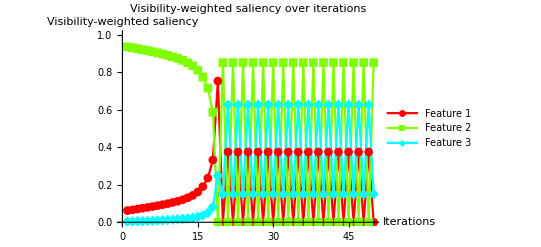

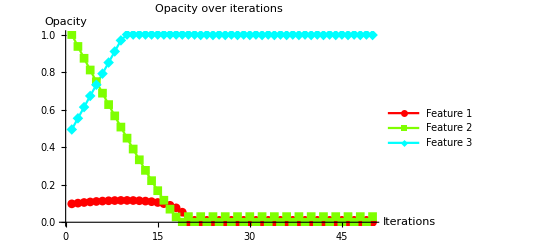

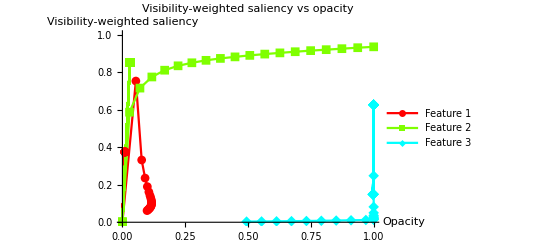

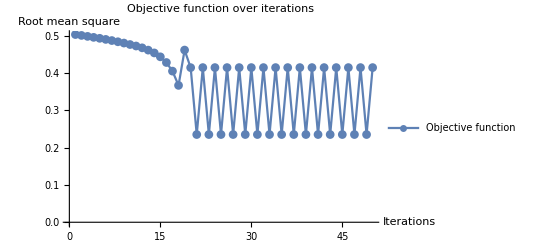

| Visibility-Weighted Saliency | Opacity | Root Mean Square | Steps | 
1 | 0.0619607
0.934603
0.00343598 | 0.0980392
1.
0.494118 | 0.503341 | 0.00380393
-0.0634603
0.0596564 | -0.0760786
1.26921
-1.19313
2 | 0.0659797
0.929892
0.00412778 | 0.101843
0.93654
0.553774 | 0.500994 | 0.00340203
-0.0629892
0.0595872 | -0.0680406
1.25978
-1.19174
3 | 0.0703983
0.924708
0.0048938 | 0.105245
0.87355
0.613361 | 0.498427 | 0.00296017
-0.0624708
0.0595106 | -0.0592035
1.24942
-1.19021
4 | 0.0748053
0.919441
0.00575349 | 0.108205
0.81108
0.672872 | 0.495806 | 0.00251947
-0.0619441
0.0594247 | -0.0503894
1.23888
-1.18849
5 | 0.0789717
0.914357
0.00667084 | 0.110725
0.749136
0.732297 | 0.49326 | 0.00210283
-0.0614357
0.0593329 | -0.0420565
1.22871
-1.18666
6 | 0.083708
0.908503
0.0077891 | 0.112828
0.6877
0.791629 | 0.490325 | 0.0016292
-0.0608503
0.0592211 | -0.032584
1.21701
-1.18442
7 | 0.0886436
0.902354
0.00900263 | 0.114457
0.626849
0.850851 | 0.48725 | 0.00113564
-0.0602354
0.0590997 | -0.0227129
1.20471
-1.18199
8 | 0.0937349
0.895872
0.0103936 | 0.115592
0.566614
0.90995 | 0.48399 | 0.000626513
-0.0595872
0.0589606 | -0.0125303
1.19174
-1.17921
9 | 0.0989745
0.889021
0.0120044 | 0.116219
0.507027
0.968911 | 0.480516 | 0.000102552
-0.0589021
0.0587996 | -0.00205103
1.17804
-1.17599
10 | 0.105279
0.881048
0.0136735 | 0.116322
0.448125
1. | 0.476593 | -0.000527856
-0.0581048
0.0586326 | 0.0105571
1.1621
-1.17265
11 | 0.111785
0.872855
0.0153593 | 0.115794
0.39002
1. | 0.472619 | -0.00117855
-0.0572855
0.0584641 | 0.023571
1.14571
-1.16928
12 | 0.119881
0.862658
0.0174605 | 0.114615
0.332735
1. | 0.467736 | -0.00198812
-0.0562658
0.058254 | 0.0397624
1.12532
-1.16508
13 | 0.130266
0.849585
0.0201493 | 0.112627
0.276469
1. | 0.461587 | -0.00302656
-0.0549585
0.0579851 | 0.0605312
1.09917
-1.1597
14 | 0.142898
0.833421
0.0236812 | 0.1096
0.22151
1. | 0.454064 | -0.00428976
-0.0533421
0.0576319 | 0.0857953
1.06684
-1.15264
15 | 0.161352
0.810039
0.0286086 | 0.105311
0.168168
1. | 0.443619 | -0.00613522
-0.0510039
0.0571391 | 0.122704
1.02008
-1.14278
16 | 0.189793
0.77397
0.0362369 | 0.0991755
0.117164
1. | 0.428384 | -0.00897934
-0.047397
0.0563763 | 0.179587
0.947939
-1.12753
17 | 0.235249
0.714698
0.0500536 | 0.0901961
0.0697672
1. | 0.40526 | -0.0135249
-0.0414698
0.0549946 | 0.270497
0.829395
-1.09989
18 | 0.331666
0.586403
0.0819301 | 0.0766713
0.0282974
1. | 0.367012 | -0.0231666
-0.0286403
0.051807 | 0.463333
0.572807
-1.03614
19 | 0.752316
0.
0.247684 | 0.0535046
0.
1. | 0.461751 | -0.0652316
0.03
0.0352316 | 1.30463
-0.6
-0.704631
20 | 0.
0.85037
0.14963 | 0.
0.03
1. | 0.414625 | 0.01
-0.055037
0.045037 | -0.2
1.10074
-0.900741
21 | 0.374479
0.
0.625521 | 0.01
0.
1. | 0.235223 | -0.0274479
0.03
-0.0025521 | 0.548958
-0.6
0.051042
22 | 0.
0.850546
0.149454 | 0.
0.03
0.997448 | 0.414766 | 0.01
-0.0550546
0.0450546 | -0.2
1.10109
-0.901093
23 | 0.374479
0.
0.625521 | 0.01
0.
1. | 0.235223 | -0.0274479
0.03
-0.0025521 | 0.548958
-0.6
0.051042
24 | 0.
0.850546
0.149454 | 0.
0.03
0.997448 | 0.414766 | 0.01
-0.0550546
0.0450546 | -0.2
1.10109
-0.901093
25 | 0.374479
0.
0.625521 | 0.01
0.
1. | 0.235223 | -0.0274479
0.03
-0.0025521 | 0.548958
-0.6
0.051042
26 | 0.
0.850546
0.149454 | 0.
0.03
0.997448 | 0.414766 | 0.01
-0.0550546
0.0450546 | -0.2
1.10109
-0.901093
27 | 0.374479
0.
0.625521 | 0.01
0.
1. | 0.235223 | -0.0274479
0.03
-0.0025521 | 0.548958
-0.6
0.051042
28 | 0.
0.850546
0.149454 | 0.
0.03
0.997448 | 0.414766 | 0.01
-0.0550546
0.0450546 | -0.2
1.10109
-0.901093
29 | 0.374479
0.
0.625521 | 0.01
0.
1. | 0.235223 | -0.0274479
0.03
-0.0025521 | 0.548958
-0.6
0.051042
30 | 0.
0.850546
0.149454 | 0.
0.03
0.997448 | 0.414766 | 0.01
-0.0550546
0.0450546 | -0.2
1.10109
-0.901093
31 | 0.374479
0.
0.625521 | 0.01
0.
1. | 0.235223 | -0.0274479
0.03
-0.0025521 | 0.548958
-0.6
0.051042
32 | 0.
0.850546
0.149454 | 0.
0.03
0.997448 | 0.414766 | 0.01
-0.0550546
0.0450546 | -0.2
1.10109
-0.901093
33 | 0.374479
0.
0.625521 | 0.01
0.
1. | 0.235223 | -0.0274479
0.03
-0.0025521 | 0.548958
-0.6
0.051042
34 | 0.
0.850546
0.149454 | 0.
0.03
0.997448 | 0.414766 | 0.01
-0.0550546
0.0450546 | -0.2
1.10109
-0.901093
35 | 0.374479
0.
0.625521 | 0.01
0.
1. | 0.235223 | -0.0274479
0.03
-0.0025521 | 0.548958
-0.6
0.051042
36 | 0.
0.850546
0.149454 | 0.
0.03
0.997448 | 0.414766 | 0.01
-0.0550546
0.0450546 | -0.2
1.10109
-0.901093
37 | 0.374479
0.
0.625521 | 0.01
0.
1. | 0.235223 | -0.0274479
0.03
-0.0025521 | 0.548958
-0.6
0.051042
38 | 0.
0.850546
0.149454 | 0.
0.03
0.997448 | 0.414766 | 0.01
-0.0550546
0.0450546 | -0.2
1.10109
-0.901093
39 | 0.374479
0.
0.625521 | 0.01
0.
1. | 0.235223 | -0.0274479
0.03
-0.0025521 | 0.548958
-0.6
0.051042
40 | 0.
0.850546
0.149454 | 0.
0.03
0.997448 | 0.414766 | 0.01
-0.0550546
0.0450546 | -0.2
1.10109
-0.901093
41 | 0.374479
0.
0.625521 | 0.01
0.
1. | 0.235223 | -0.0274479
0.03
-0.0025521 | 0.548958
-0.6
0.051042
42 | 0.
0.850546
0.149454 | 0.
0.03
0.997448 | 0.414766 | 0.01
-0.0550546
0.0450546 | -0.2
1.10109
-0.901093
43 | 0.374479
0.
0.625521 | 0.01
0.
1. | 0.235223 | -0.0274479
0.03
-0.0025521 | 0.548958
-0.6
0.051042
44 | 0.
0.850546
0.149454 | 0.
0.03
0.997448 | 0.414766 | 0.01
-0.0550546
0.0450546 | -0.2
1.10109
-0.901093
45 | 0.374479
0.
0.625521 | 0.01
0.
1. | 0.235223 | -0.0274479
0.03
-0.0025521 | 0.548958
-0.6
0.051042
46 | 0.
0.850546
0.149454 | 0.
0.03
0.997448 | 0.414766 | 0.01
-0.0550546
0.0450546 | -0.2
1.10109
-0.901093
47 | 0.374479
0.
0.625521 | 0.01
0.
1. | 0.235223 | -0.0274479
0.03
-0.0025521 | 0.548958
-0.6
0.051042
48 | 0.
0.850546
0.149454 | 0.
0.03
0.997448 | 0.414766 | 0.01
-0.0550546
0.0450546 | -0.2
1.10109
-0.901093
49 | 0.374479
0.
0.625521 | 0.01
0.
1. | 0.235223 | -0.0274479
0.03
-0.0025521 | 0.548958
-0.6
0.051042
50 | 0.
0.850546
0.149454 | 0.
0.03
0.997448 | 0.414766 | 0.01
-0.0550546
0.0450546 | -0.2
1.10109
-0.901093

```mathematica
t2-t1
iteration
saliency1=ListLinePlot[Transpose[#&@@@list],PlotLegends->{"Feature 1","Feature 2","Feature 3","Feature 4"},PlotLabel->"Visibility-weighted saliency over iterations",PlotRange->{All,{0,1}},PlotStyle->chartcolors,PlotMarkers->Automatic,AxesLabel->{"Iterations","Visibility-weighted saliency"}]
Export[plotpath<>dataname<>"_saliency_fixed.png",saliency1];
opacity1=ListLinePlot[Transpose[#2&@@@list],PlotLegends->{"Feature 1","Feature 2","Feature 3","Feature 4"},PlotLabel->"Opacity over iterations",PlotRange->{All,{0,1}},PlotStyle->chartcolors,PlotMarkers->Automatic,AxesLabel->{"Iterations","Opacity"}]
Export[plotpath<>dataname<>"_opacity_fixed.png",opacity1];
x=Transpose[#2&@@@list];
y=Transpose[#&@@@list];
(*ListLinePlot[{Transpose[{x[[1]],y[[1]]}],Transpose[{x[[2]],y[[2]]}],Transpose[{x[[3]],y[[3]]}]},PlotStyle->chartcolors,PlotLabel->"Visibility-weighted saliency vs opacity",AxesLabel->{"Opacity","Visibility-weighted saliency"},PlotLegends->{"Feature 1","Feature 2","Feature 3","Feature 4"},PlotRange->{{0,1},{0,1}},PlotMarkers->Automatic]*)
saliencyopacity1=ListLinePlot[Transpose[{x[[#]],y[[#]]}]&/@Range[Length[chartcolors]],PlotStyle->chartcolors,PlotLabel->"Visibility-weighted saliency vs opacity",AxesLabel->{"Opacity","Visibility-weighted saliency"},PlotLegends->{"Feature 1","Feature 2","Feature 3","Feature 4"},PlotRange->{{0,1},{0,1}},PlotMarkers->Automatic]
Export[plotpath<>dataname<>"_saliencyopacity_fixed.png",saliencyopacity1];
rmslist1=#3&@@@list;
rms1=ListLinePlot[#3&@@@list,PlotLegends->{"Objective function"},PlotLabel->"Objective function over iterations",PlotRange->{All,All},PlotMarkers->Automatic,AxesLabel->{"Iterations","Root mean square"}]
Export[plotpath<>dataname<>"_rms_fixed.png",rms1];
table1=TableForm[list,TableHeadings->{Automatic,{"Visibility-Weighted Saliency","Opacity", "Root Mean Square","Steps"}},TableSpacing->{2,3}]
Export[plotpath<>dataname<>"_table_fixed.png",table1];
path1=#2&@@@list;
AppendTo[records,{t2-t1,iteration,Last[path1]}];
```

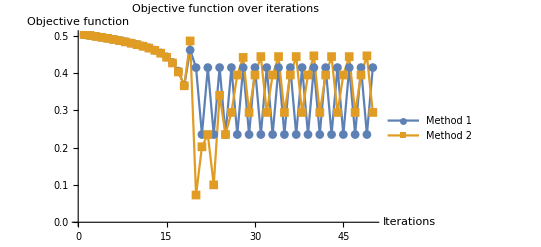

```mathematica
rmslists1=ListLinePlot[{rmslist1,rmslist5},PlotLegends->{"Method 1","Method 2"},PlotLabel->"Objective function over iterations",PlotRange->{All,All},PlotMarkers->Automatic,AxesLabel->{"Iterations","Objective function"}]
Export[plotpath<>dataname<>"_rms_fixed_newton.png",rmslists1];
```

```mathematica
(*reset peak control points*)
alpha0[[#]]&/@index0;
peaks=alpha[[#]]&/@index;
MapIndexed[(alpha0[[#]]=peaks[[First@#2]])&,index0];
(*parallel gradient*)
multipliers={1,2,4,8};
previous={0,0,0};
iteration=0;
t1=AbsoluteTime[];
t2=0;
list=Table[Module[{peaks,mean,steps,rms,meanlist,peaklist,rmslist,minindex},
mean=If[Norm[previous]>0,previous,Visibility[Interpolation[Transpose[{intensity0,alpha0}],InterpolationOrder->1]]];
rms=RootMeanSquare[mean-target];
peaks=alpha0[[#]]&/@index0;
steps=-2*(mean-target)*stepsize;
peaklist=ParallelMap[Clip[peaks+steps*#,{0,1}]&,multipliers];
meanlist=ParallelMap[VisibilitySaliency[#]&,peaklist];
rmslist=ParallelMap[RootMeanSquare[#-target]&,meanlist];
minindex=First@Ordering[rmslist,1];
MapIndexed[(alpha0[[#]]=peaklist[[minindex]][[First@#2]])&,index0];
previous=meanlist[[minindex]];
If[t2==0 && rmslist[[minindex]]<epsilon,t2=AbsoluteTime[];iteration=iterator];
{mean,peaks,rms,steps,multipliers[[minindex]]}
],{iterator,10}];
```

-3.6537588950038183×10^9

0

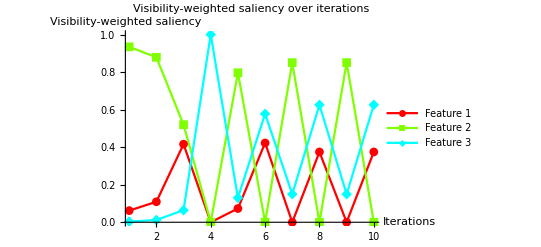

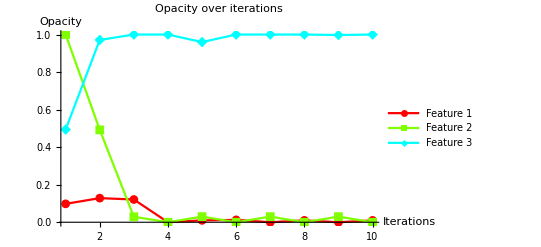

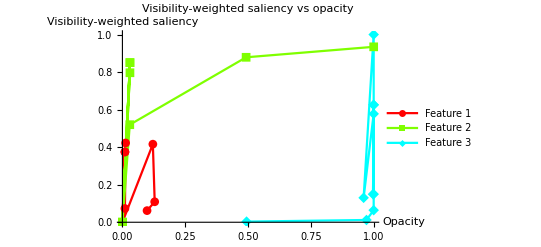

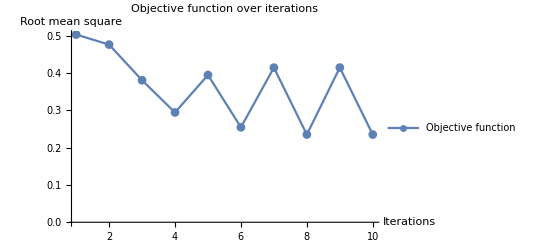

| Visibility-Weighted Saliency | Opacity | Root Mean Square | Steps | Multiplier
1 | 0.0619607
0.934603
0.00343598 | 0.0980392
1.
0.494118 | 0.503341 | 0.00380393
-0.0634603
0.0596564 | 8
2 | 0.109129
0.878808
0.0120634 | 0.128471
0.492317
0.971369 | 0.476365 | -0.000912902
-0.0578808
0.0587937 | 8
3 | 0.415961
0.519716
0.0643234 | 0.121167
0.0292713
1. | 0.380813 | -0.0315961
-0.0219716
0.0535677 | 4
4 | 0.
0.
1. | 0.
0.
1. | 0.294392 | 0.01
0.03
-0.04 | 1
5 | 0.073244
0.796452
0.130304 | 0.01
0.03
0.96 | 0.394882 | 0.0026756
-0.0496452
0.0469696 | 1
6 | 0.422343
0.
0.577657 | 0.0126756
0.
1. | 0.254561 | -0.0322343
0.03
0.0022343 | 1
7 | 0.
0.85037
0.14963 | 0.
0.03
1. | 0.414625 | 0.01
-0.055037
0.045037 | 1
8 | 0.374479
0.
0.625521 | 0.01
0.
1. | 0.235223 | -0.0274479
0.03
-0.0025521 | 1
9 | 0.
0.850546
0.149454 | 0.
0.03
0.997448 | 0.414766 | 0.01
-0.0550546
0.0450546 | 1
10 | 0.374479
0.
0.625521 | 0.01
0.
1. | 0.235223 | -0.0274479
0.03
-0.0025521 | 1

```mathematica
t2-t1
iteration
saliency2=ListLinePlot[Transpose[#&@@@list],PlotLegends->{"Feature 1","Feature 2","Feature 3","Feature 4"},PlotLabel->"Visibility-weighted saliency over iterations",PlotRange->{All,{0,1}},PlotStyle->chartcolors,PlotMarkers->Automatic,AxesLabel->{"Iterations","Visibility-weighted saliency"}]
Export[plotpath<>dataname<>"_saliency_parallelsearch.png",saliency2];
opacity2=ListLinePlot[Transpose[#2&@@@list],PlotLegends->{"Feature 1","Feature 2","Feature 3","Feature 4"},PlotLabel->"Opacity over iterations",PlotRange->{All,{0,1}},PlotStyle->chartcolors,PlotMarkers->Automatic,AxesLabel->{"Iterations","Opacity"}]
Export[plotpath<>dataname<>"_opacity_parallelsearch.png",opacity2];
x=Transpose[#2&@@@list];
y=Transpose[#&@@@list];
(*ListLinePlot[{Transpose[{x[[1]],y[[1]]}],Transpose[{x[[2]],y[[2]]}],Transpose[{x[[3]],y[[3]]}]},PlotStyle->chartcolors,PlotLabel->"Visibility-weighted saliency vs opacity",AxesLabel->{"Opacity","Visibility-weighted saliency"},PlotLegends->{"Feature 1","Feature 2","Feature 3","Feature 4"},PlotRange->{{0,1},{0,1}},PlotMarkers->Automatic]*)
saliencyopacity2=ListLinePlot[Transpose[{x[[#]],y[[#]]}]&/@Range[Length[chartcolors]],PlotStyle->chartcolors,PlotLabel->"Visibility-weighted saliency vs opacity",AxesLabel->{"Opacity","Visibility-weighted saliency"},PlotLegends->{"Feature 1","Feature 2","Feature 3","Feature 4"},PlotRange->{{0,1},{0,1}},PlotMarkers->Automatic]
Export[plotpath<>dataname<>"_saliencyopacity_parallelsearch.png",saliencyopacity2];
rmslist2=#3&@@@list;
rms2=ListLinePlot[#3&@@@list,PlotLegends->{"Objective function"},PlotLabel->"Objective function over iterations",PlotRange->{All,All},PlotMarkers->Automatic,AxesLabel->{"Iterations","Root mean square"}]
Export[plotpath<>dataname<>"_rms_parallelsearch.png",rms2];
table2=TableForm[list,TableHeadings->{Automatic,{"Visibility-Weighted Saliency","Opacity", "Root Mean Square","Steps","Multiplier"}},TableSpacing->{2,3}]
Export[plotpath<>dataname<>"_table_parallelsearch.png",table2];
path2=#2&@@@list;
AppendTo[records,{t2-t1,iteration,Last[path2]}];
```

```mathematica
(*reset peak control points*)
alpha0[[#]]&/@index0;
peaks=alpha[[#]]&/@index;
MapIndexed[(alpha0[[#]]=peaks[[First@#2]])&,index0];
(*line search*)
previous={0,0,0};
iteration=0;
t1=AbsoluteTime[];
t2=0;
list=Table[Module[{peaks,mean,steps,rms,peaklist,minindex,minrms,minmean,rms2,mean2},
mean=If[Norm[previous]>0,previous,Visibility[Interpolation[Transpose[{intensity0,alpha0}],InterpolationOrder->1]]];
rms=RootMeanSquare[mean-target];
peaks=alpha0[[#]]&/@index0;
steps=-2*(mean-target)*stepsize;
peaklist=Map[Clip[peaks+steps*#,{0,1}]&,multipliers];
minindex=1;
minmean=VisibilitySaliency[peaklist[[minindex]]];
minrms=RootMeanSquare[minmean-target];
Do[mean2=VisibilitySaliency[peaklist[[i]]];
rms2=RootMeanSquare[mean2-target];
If[rms2<minrms,minrms=rms2;minmean=mean2;minindex=i,Return[i]];
,{i,Range[2,4]}];
MapIndexed[(alpha0[[#]]=peaklist[[minindex]][[First@#2]])&,index0];
previous=minmean;
If[t2==0 && minrms<epsilon,t2=AbsoluteTime[];iteration=iterator];
{mean,peaks,rms,steps,multipliers[[minindex]]}
],{iterator,10}];
```

-3.6537589165494732×10^9

0

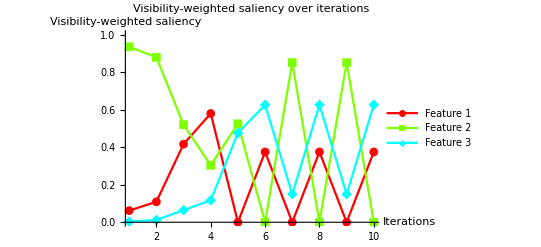

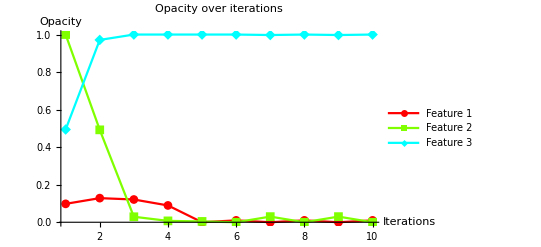

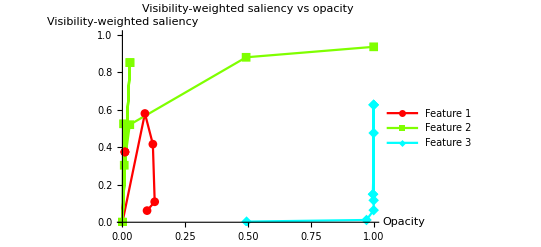

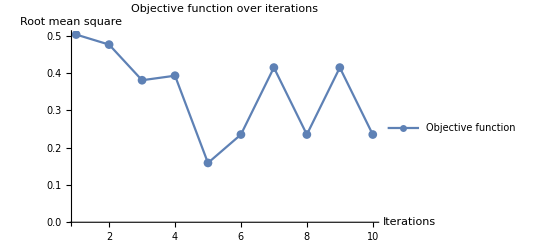

| Visibility-Weighted Saliency | Opacity | Root Mean Square | Steps | Multiplier
1 | 0.0619607
0.934603
0.00343598 | 0.0980392
1.
0.494118 | 0.503341 | 0.00380393
-0.0634603
0.0596564 | 8
2 | 0.109129
0.878808
0.0120634 | 0.128471
0.492317
0.971369 | 0.476365 | -0.000912902
-0.0578808
0.0587937 | 8
3 | 0.415961
0.519716
0.0643234 | 0.121167
0.0292713
1. | 0.380813 | -0.0315961
-0.0219716
0.0535677 | 1
4 | 0.579469
0.303672
0.116859 | 0.0895714
0.00729969
1. | 0.392992 | -0.0479469
-0.000367248
0.0483141 | 8
5 | 0.
0.52451
0.47549 | 0.
0.00436171
1. | 0.159068 | 0.01
-0.022451
0.012451 | 1
6 | 0.374479
0.
0.625521 | 0.01
0.
1. | 0.235223 | -0.0274479
0.03
-0.0025521 | 1
7 | 0.
0.850546
0.149454 | 0.
0.03
0.997448 | 0.414766 | 0.01
-0.0550546
0.0450546 | 1
8 | 0.374479
0.
0.625521 | 0.01
0.
1. | 0.235223 | -0.0274479
0.03
-0.0025521 | 1
9 | 0.
0.850546
0.149454 | 0.
0.03
0.997448 | 0.414766 | 0.01
-0.0550546
0.0450546 | 1
10 | 0.374479
0.
0.625521 | 0.01
0.
1. | 0.235223 | -0.0274479
0.03
-0.0025521 | 1

```mathematica
t2-t1
iteration
saliency3=ListLinePlot[Transpose[#&@@@list],PlotLegends->{"Feature 1","Feature 2","Feature 3","Feature 4"},PlotLabel->"Visibility-weighted saliency over iterations",PlotRange->{All,{0,1}},PlotStyle->chartcolors,PlotMarkers->Automatic,AxesLabel->{"Iterations","Visibility-weighted saliency"}]
Export[plotpath<>dataname<>"_saliency_linesearch.png",saliency3];
opacity3=ListLinePlot[Transpose[#2&@@@list],PlotLegends->{"Feature 1","Feature 2","Feature 3","Feature 4"},PlotLabel->"Opacity over iterations",PlotRange->{All,{0,1}},PlotStyle->chartcolors,PlotMarkers->Automatic,AxesLabel->{"Iterations","Opacity"}]
Export[plotpath<>dataname<>"_opacity_linesearch.png",opacity3];
x=Transpose[#2&@@@list];
y=Transpose[#&@@@list];
(*ListLinePlot[{Transpose[{x[[1]],y[[1]]}],Transpose[{x[[2]],y[[2]]}],Transpose[{x[[3]],y[[3]]}]},PlotStyle->chartcolors,PlotLabel->"Visibility-weighted saliency vs opacity",AxesLabel->{"Opacity","Visibility-weighted saliency"},PlotLegends->{"Feature 1","Feature 2","Feature 3","Feature 4"},PlotRange->{{0,1},{0,1}},PlotMarkers->Automatic]*)
saliencyopacity3=ListLinePlot[Transpose[{x[[#]],y[[#]]}]&/@Range[Length[chartcolors]],PlotStyle->chartcolors,PlotLabel->"Visibility-weighted saliency vs opacity",AxesLabel->{"Opacity","Visibility-weighted saliency"},PlotLegends->{"Feature 1","Feature 2","Feature 3","Feature 4"},PlotRange->{{0,1},{0,1}},PlotMarkers->Automatic]
Export[plotpath<>dataname<>"_saliencyopacity_linesearch.png",saliencyopacity3];
rmslist3=#3&@@@list;
rms3=ListLinePlot[#3&@@@list,PlotLegends->{"Objective function"},PlotLabel->"Objective function over iterations",PlotRange->{All,All},PlotMarkers->Automatic,AxesLabel->{"Iterations","Root mean square"}]
Export[plotpath<>dataname<>"_rms_linesearch.png",rms3];
table3=TableForm[list,TableHeadings->{Automatic,{"Visibility-Weighted Saliency","Opacity", "Root Mean Square","Steps","Multiplier"}},TableSpacing->{2,3}]
Export[plotpath<>dataname<>"_table_linesearch.png",table3];
path3=#2&@@@list;
AppendTo[records,{t2-t1,iteration,Last[path3]}];
```

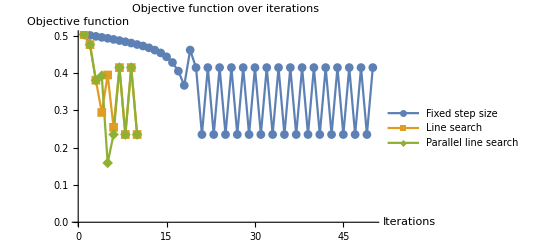

```mathematica
rmslists2=ListLinePlot[{rmslist1,rmslist2,rmslist3},PlotLegends->{"Fixed step size","Line search","Parallel line search"},PlotLabel->"Objective function over iterations",PlotRange->{All,All},PlotMarkers->Automatic,AxesLabel->{"Iterations","Objective function"}]
Export[plotpath<>dataname<>"_rms_fixed_linesearch_parallel.png",rmslists2];
```

```mathematica
(*(* compare the performance of 3 methods for computing visibility-weighted saliency *)
n=10;

t=Table[AbsoluteTiming[
peaks={0.1,0.3,0.6};
alpha2=alpha0;
MapIndexed[(alpha2[[#]]=peaks[[First@#2]])&,index0];
fun=Interpolation[Transpose[{intensity0,alpha2}],InterpolationOrder->1];
vis=Block[{f=fun,data=d},renderslices2[face]];
viss=ParallelMap[ImageMultiply[#,vis]&,{g1,g2}];
total=ParallelMap[ImageMeasurements[#,"TotalIntensity"]&,viss];
vs=ParallelTable[Table[If[total[[j]]≠0,ImageMeasurements[ImageMultiply[viss[[j]],i],"TotalIntensity"]/total[[j]],0],{i,features}],{j,Length[total]}];
mean=Mean[vs]
],{n}];
Total[#&@@@t]/n

t=Table[AbsoluteTiming[
peaks={0.1,0.3,0.6};
alpha2=alpha0;
MapIndexed[(alpha2[[#]]=peaks[[First@#2]])&,index0];
fun=Interpolation[Transpose[{intensity0,alpha2}],InterpolationOrder->1];
vis=Block[{f=fun,data=d},renderslices2[face]];
viss=ImageMultiply[g1,vis];(* weighted by lightness DoG (difference of Gaussians) *)
(*vs=Table[ImageMeasurements[ImageMultiply[viss,i],"TotalIntensity"]/ImageMeasurements[viss,"TotalIntensity"],{i,features}];*)
total=ImageMeasurements[viss,"TotalIntensity"];
vs=ParallelTable[If[total≠0,ImageMeasurements[ImageMultiply[viss,i],"TotalIntensity"]/total,0],{i,features}];
viss2=ImageMultiply[g2,vis];(* weighted by chroma DoG *)
(*vs2=Table[ImageMeasurements[ImageMultiply[viss2,i],"TotalIntensity"]/ImageMeasurements[viss2,"TotalIntensity"],{i,features}];*)
total2=ImageMeasurements[viss2,"TotalIntensity"];
vs2=ParallelTable[If[total2≠0,ImageMeasurements[ImageMultiply[viss2,i],"TotalIntensity"]/total2,0],{i,features}];
mean=Mean[{vs,vs2}]
],{n}];
Total[#&@@@t]/n

t=Table[AbsoluteTiming[
peaks={0.1,0.3,0.6};
alpha2=alpha0;
MapIndexed[(alpha2[[#]]=peaks[[First@#2]])&,index0];
fun=Interpolation[Transpose[{intensity0,alpha2}],InterpolationOrder->1];
vis=Block[{f=fun,data=d},renderslices2[face]];
viss=Map[ImageMultiply[#,vis]&,{g1,g2}];
total=Map[ImageMeasurements[#,"TotalIntensity"]&,viss];
vs=Table[Table[If[total[[j]]≠0,ImageMeasurements[ImageMultiply[viss[[j]],i],"TotalIntensity"]/total[[j]],0],{i,features}],{j,Length[total]}];
mean=Mean[vs]
],{n}];
Total[#&@@@t]/n*)
```

```mathematica
(*(*reset peak control points*)
alpha0[[#]]&/@index0;
peaks=alpha[[#]]&/@index;
MapIndexed[(alpha0[[#]]=peaks[[First@#2]])&,index0];
(*gradient descent with fixed step size*)
iteration=0;
previous={0,{0,0,0},{0,0,0}};
t1=AbsoluteTime[];
t2=0;
list=Table[Module[{peaks,mean,steps,rms,peaks0,gradient},
mean=Visibility[Interpolation[Transpose[{intensity0,alpha0}],InterpolationOrder->1]];
rms=RootMeanSquare[mean-target];
peaks=alpha0[[#]]&/@index0;
gradient:=2*(mean-target);
(*steps=If[First@previous==0,-gradient*stepsize,Module[{rms0,mean0,p0,dy,dx},
{rms0,mean0,p0}=previous;
dy=Table[RootMeanSquare[Table[If[i==n,mean0[[i]],mean[[i]]],{i,Length[mean]}]-target],{n,Length[mean]}];
dx=peaks-p0;
If[Product[i,{i,dx}]≠0,-dy/dx*stepsize,-gradient*stepsize]
]];*)
steps=If[First@previous==0,-gradient*stepsize,Module[{rms0,mean0,p0,dy,dx},
{rms0,mean0,p0}=previous;
dy=mean-mean0;
dx=peaks-p0;
If[Product[i,{i,dx}]≠0,-dy/dx*gradient*stepsize,-gradient*stepsize]
]];
previous={rms,mean,peaks};
peaks0=peaks;
peaks=Clip[peaks+steps,{0,1}];
MapIndexed[(alpha0[[#]]=peaks[[First@#2]])&,index0];
If[t2==0 && rms<epsilon,t2=AbsoluteTime[];iteration=iterator];
{mean,peaks0,rms,steps}
],{iterator,10}];*)
```

```mathematica
(*t2-t1
iteration
saliency4=ListLinePlot[Transpose[#&@@@list],PlotLegends->{"Feature 1","Feature 2","Feature 3","Feature 4"},PlotLabel->"Visibility-weighted saliency over iterations",PlotRange->{All,{0,1}},PlotStyle->chartcolors,PlotMarkers->Automatic,AxesLabel->{"Iterations","Visibility-weighted saliency"}]
Export[plotpath<>dataname<>"_saliency_difference.png",saliency4];
opacity4=ListLinePlot[Transpose[#2&@@@list],PlotLegends->{"Feature 1","Feature 2","Feature 3","Feature 4"},PlotLabel->"Opacity over iterations",PlotRange->{All,{0,1}},PlotStyle->chartcolors,PlotMarkers->Automatic,AxesLabel->{"Iterations","Opacity"}]
Export[plotpath<>dataname<>"_opacity_difference.png",opacity4];
x=Transpose[#2&@@@list];
y=Transpose[#&@@@list];
(*ListLinePlot[{Transpose[{x[[1]],y[[1]]}],Transpose[{x[[2]],y[[2]]}],Transpose[{x[[3]],y[[3]]}]},PlotStyle->chartcolors,PlotLabel->"Visibility-weighted saliency vs opacity",AxesLabel->{"Opacity","Visibility-weighted saliency"},PlotLegends->{"Feature 1","Feature 2","Feature 3","Feature 4"},PlotRange->{{0,1},{0,1}},PlotMarkers->Automatic]*)
saliencyopacity4=ListLinePlot[Transpose[{x[[#]],y[[#]]}]&/@Range[Length[chartcolors]],PlotStyle->chartcolors,PlotLabel->"Visibility-weighted saliency vs opacity",AxesLabel->{"Opacity","Visibility-weighted saliency"},PlotLegends->{"Feature 1","Feature 2","Feature 3","Feature 4"},PlotRange->{{0,1},{0,1}},PlotMarkers->Automatic]
Export[plotpath<>dataname<>"_saliencyopacity_difference.png",saliencyopacity4];
rms4=ListLinePlot[#3&@@@list,PlotLegends->{"Objective function"},PlotLabel->"Objective function over iterations",PlotRange->{All,All},PlotMarkers->Automatic,AxesLabel->{"Iterations","Root mean square"}]
Export[plotpath<>dataname<>"_rms_difference.png",rms4];
table4=TableForm[list,TableHeadings->{Automatic,{"Visibility-Weighted Saliency","Opacity", "Root Mean Square","Steps"}},TableSpacing->{2,3}]
Export[plotpath<>dataname<>"_table_difference.png",table4];
path4=#2&@@@list;
AppendTo[records,{t2-t1,iteration,Last[path4]}];*)
```

```mathematica
recordxml=plotpath<>"records.xml";
recordmap=If[FileExistsQ[recordxml],Association@Import[recordxml],<||>];
AssociateTo[recordmap,dataname->records];
Export[recordxml,Normal[recordmap]];
dataname->records
```

vismale_strong_green→{{-3.6537587901661791×10^9,0,{0.000524724,0.,1.}},{-3.6537588426626068×10^9,0,{0.,0.03,0.997448}},{-3.6537588950038183×10^9,0,{0.01,0.,1.}},{-3.6537589165494732×10^9,0,{0.01,0.,1.}}}

```mathematica
ObjectiveFunction[pos_]:=RootMeanSquare[VisibilitySaliency[pos]-target];
```

```mathematica
(*ObjectiveFunction[{0.1,0.3,0.6}]
(*FindMinimum[{ObjectiveFunction[{x1,x2,x3}],0≤x1≤1,0≤x2≤1,0≤x3≤1},{{x1,{0.1}},{x2,{0.3}},{x3,{0.6}}}]*)
FindMinimum[x1 Cos[x1]+x2 Cos[x2],{{x1,0},{x2,0}}]
Plot3D[x1 Sin[x1]+x2 Sin[x2],{x1,0,10},{x2,0,10}]*)
```

```mathematica
(*range=Range[0,1,0.1];
coordinates=Flatten[Table[{i,j,k},{i,range},{j,range},{k,range}],2];
Length[coordinates]
AbsoluteTiming[
searchspace=ParallelTable[Module[{mean,rms},
mean=VisibilitySaliency[c];
rms=RootMeanSquare[mean-target];
{mean,c,rms}
],{c,coordinates}];
]*)
```

```mathematica
(*transform=RotationTransform[-90 Degree,{0,0,1}];
vec=transform[{1.3, -2.4, 2.}];
opacitylist=#2&@@@searchspace;
rmslist=#3&@@@searchspace;
merged=ParallelTable[Append[opacitylist[[i]],rmslist[[i]]],{i,Length[opacitylist]}];
densityplot=ListDensityPlot3D[merged,ColorFunction->"LightTemperatureMap",PlotLegends->Automatic,PlotLabel->{"x","y","z"},PlotTheme->"Detailed",OpacityFunction->Automatic];
paths={path1,path3};
pathcolors={Red,Green,Blue};
plotlegends={{"Fixed step size"},{"Adaptive step size with line search"},{"Adaptive step size with parallel search"}};
pointplots=ParallelTable[ListPointPlot3D[paths[[i]],PlotStyle->{pathcolors[[i]],Thick,PointSize[Large]},PlotLegends->plotlegends[[i]]],{i,Length[paths]}];
lineplots=ParallelTable[ListPointPlot3D[paths[[i]],PlotStyle->{pathcolors[[i]]}]/.Point->Line,{i,Length[paths]}];
sp=Show[densityplot,PlotLabel->"Objective function in parameter space",ViewPoint->vec]
sp2=Show[densityplot,pointplots[[1]],pointplots[[2]],lineplots[[1]],lineplots[[2]],PlotLabel->"Gradient descent in parameter space",ViewPoint->vec]
Export[plotpath<>dataname<>"_parameterspace.png",sp];
Export[plotpath<>dataname<>"_parameterspace_path.png",sp2];

{c1,c2,c3}=chartcolors;
blend1=Blend[{{0,Black},{0.5,c1},{1,White}},#]&;
blend2=Blend[{{0,Black},{0.5,c2},{1,White}},#]&;
blend3=Blend[{{0,Black},{0.5,c3},{1,White}},#]&;
saliencylist=#&@@@searchspace;
first=#&@@@saliencylist;
second=#2&@@@saliencylist;
third=#3&@@@saliencylist;
merged1=ParallelTable[Append[opacitylist[[i]],first[[i]]],{i,Length[opacitylist]}];
merged2=ParallelTable[Append[opacitylist[[i]],second[[i]]],{i,Length[opacitylist]}];
merged3=ParallelTable[Append[opacitylist[[i]],third[[i]]],{i,Length[opacitylist]}];
dplots=ListDensityPlot3D[#1,ColorFunction->#2,PlotLegends->Automatic,PlotTheme->"Detailed",OpacityFunction->(#&)]&@@@{{merged1,blend1},{merged2,blend2},{merged3,blend3}};
densityplots=MapIndexed[Show[#,PlotLabel->"Visibility-weighted saliency of feature "<>ToString[First@#2],ViewPoint->vec]&,dplots]
MapIndexed[Export[plotpath<>dataname<>"_densityplot"<>ToString[First@#2]<>".png",#]&,densityplots];*)
```

```mathematica
saveTransferFunction[peaks_,filename_]:=Module[{a2,rgba2,intensity2,rgbafunction2,rgba2denormalized,xrgba,strlist,alphaMode,gammaValue,domain,threshold,k,int,split,colorL,keylist,keys,TransFuncIntensity,VoreenData,xml},
MapIndexed[(alpha0[[#]]=peaks[[First@#2]])&,index0];
a2=IntegerPart[255*alpha0[[#]]]&/@rangeOfAlpha;
rgba2=(#/255.&)/@Transpose[{r,g,b,a2}]//(RGBColor/@#&);
intensity2=intensity0[[#]]&/@rangeOfAlpha;
rgbafunction2=(Blend[Transpose[{intensity2,rgba2}], #] & );(* for return only. not used in this function *)

rgba2denormalized=Transpose[{r,g,b,a2}];
xrgba=Table[Join[{intensity2[[i]]},rgba2denormalized[[i]]],{i,Length[intensity2]}];
strlist={ToString[#1],ToString[#2],ToString[#3],ToString[#4],ToString[#5]}&@@@xrgba;
alphaMode=XMLElement["alphaMode",{"value"->"1"},{}];
gammaValue=XMLElement["gammaValue",{"value"->"1"},{}];
domain=XMLElement["domain",{"x"->"0","y"->"1"},{}];
threshold=XMLElement["threshold",{"x"->"0","y"->"1"},{}];
k=({int=XMLElement["intensity",{"value"->#1},{}],split=XMLElement["split",{"value"->"false"},{}],colorL=XMLElement["colorL",{"r"->#2,"g"->#3,"b"->#4,"a"->#5},{}]}&)@@@strlist;
keylist=XMLElement["key",{"type"->"TransFuncMappingKey"},{#1,#2,#3}]&@@@k;
keys=XMLElement["Keys",{},keylist];
TransFuncIntensity=XMLElement["TransFuncIntensity",{"type"->"TransFuncIntensity"},{alphaMode,gammaValue,domain,threshold,keys}];
VoreenData=XMLElement["VoreenData",{"version"->"1"},{TransFuncIntensity}];
xml=XMLObject["Document"][{XMLObject["Declaration"]["Version"->"1.0"],XMLObject["Comment"]["This is a Voreen transfer function exported from Mathematica"]},VoreenData,{}];
Export[filename,xml, "XML"];
rgbafunction2
];
```

```mathematica
tf1=saveTransferFunction[Last[path1],plotpath<>dataname<>"_optimized_fixed.tfi"];
tf2=saveTransferFunction[Last[path2],plotpath<>dataname<>"_optimized_parallelsearch.tfi"];
tf3=saveTransferFunction[Last[path3],plotpath<>dataname<>"_optimized_linesearch.tfi"];
Image3D[d,ColorFunction->rgbafunction,ViewPoint->viewpoints[face]]
Image3D[d,ColorFunction->tf3,ViewPoint->viewpoints[face]]
ListLinePlot[Transpose[{intensity,alpha}],PlotRange->{{0,1},{0,1}},ColorFunction->rgbfunction,PlotLegends->"Before optimization"]
(*Transpose[{intensity,r,g,b,a}]*)
ListLinePlot[Transpose[{intensity0[[#]]&/@rangeOfAlpha,alpha0[[#]]&/@rangeOfAlpha}],PlotRange->{{0,1},{0,1}},ColorFunction->rgbfunction,PlotLegends->"After optimization"]
(*xrgba*)
```

-Graphics-

-Graphics-